```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
```

CloudConnect::clver: Connecting to a cloud running an earlier version of the Wolfram Engine: 12.0

```mathematica
ts=ds[Select[#Country["Name"]==="China"&],<|"region"->First@StringSplit[#AdministrativeDivision["Name"],", "],"cases"->#ConfirmedCases["LastValue"]|>&];
```

```mathematica
cases=ts[ReverseSortBy[#cases&]]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\docs\\cases.csv",cases,"TextDelimiters"->""]
```

D:\git\wolfram-coronavirus\docs\cases.csv

```mathematica
ds
```

```mathematica
ts=ds[Select[(#Country["Name"]=!="China"&&Not[MissingQ[#Country]])&],<|"country"->First@StringSplit[#Country["Name"],", "],"cases"->#ConfirmedCases["LastValue"]|>&];
```

```mathematica
ts2=ts[GroupBy[#country&],<|"country"->First[#]["country"],"cases"->Total[Map[#["cases"]&,#]]|>&]
```

```mathematica
cases=ts2[ReverseSortBy[#cases&]]
```

```mathematica
Export["D:\\git\\wolfram-coronavirus\\docs\\cases-by-country.csv",c2,"TextDelimiters"->""]
```

D:\git\wolfram-coronavirus\docs\cases-by-country.csv

```mathematica
c2=cases[Values]
```

```mathematica
ExportString[c2,"TextDelimiters"->""]
```

ExportString::argr: ExportString called with 1 argument; 2 arguments are expected.

```mathematica
ds[Select[#Country["Name"]==="Australia"&]]
```

```mathematica
ts=ds[Select[#AdministrativeDivision==Entity["AdministrativeDivision",{"Hubei","China"}]&],"ConfirmedCases"]//Normal//First
```

TimeSeries[…]

```mathematica
TimeSeriesRescale[ts,{DateObject[{2020,1,21}],DateObject[{2020,2,9}],"Day"}]
```

TimeSeries[…]

```mathematica
ts2=TimeSeriesResample[ts,"Day"]
```

TimeSeries[…]

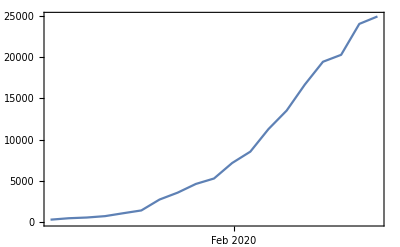

```mathematica
DateListPlot[ts2]
```

```mathematica
ts3=Map[<|"day"->DateString[First[#],{"MonthName"," ","Day"}],"cases"->Round[Last[#]]|>&,N[Normal[ts2]]]
```

{<|day→January 21,cases→270|>,<|day→January 22,cases→444|>,<|day→January 23,cases→532|>,<|day→January 24,cases→699|>,<|day→January 25,cases→1052|>,<|day→January 26,cases→1393|>,<|day→January 27,cases→2714|>,<|day→January 28,cases→3554|>,<|day→January 29,cases→4609|>,<|day→January 30,cases→5271|>,<|day→January 31,cases→7153|>,<|day→February 01,cases→8533|>,<|day→February 02,cases→11275|>,<|day→February 03,cases→13522|>,<|day→February 04,cases→16678|>,<|day→February 05,cases→19452|>,<|day→February 06,cases→20293|>,<|day→February 07,cases→24048|>,<|day→February 08,cases→24953|>}

```mathematica
Export["D:\\git\\wolfram-coronavirus\\docs\\wuhan-timeline.csv",Dataset[ts3]]
```

D:\git\wolfram-coronavirus\docs\wuhan-timeline.csv

```mathematica
ScheduledTask
```

```mathematica
$Version
```

12.1.0 for Microsoft Windows (64-bit) (January 21, 2020)